```mathematica
ClearAll[σz, σ0, σx]
σz = PauliMatrix[3];
σ0 = PauliMatrix[0];
σx = PauliMatrix[1];

createSigmaZ[L_,j_]:=Module[{full,m},If[j==0,full=σz,full=σ0];
For[m=1,m<L,m++,If[m≠j,full=KroneckerProduct[full,σ0],full=KroneckerProduct[full,σz]]];
Return[full]]

createSigmaXs[L_,j_]:=Module[{full,m},If[j==0||j==L-1,full=σx,full=σ0];
For[m=1,m<L,m++,If[m==j||m==j+1,full=KroneckerProduct[full,σx],full=KroneckerProduct[full,σ0]]];
Return[full]]
createSigmaX[L_,j_]:=Module[{full,m},If[j==0,full=σx,full=σ0];
For[m=1,m<L,m++,If[m≠j,full=KroneckerProduct[full,σ0],full=KroneckerProduct[full,σx]]];
Return[full]]

genHamiltonian[L_,g_,J_]:=Module[{H,s},H=0;
For[s=0,s<L,s++,H=H-g*createSigmaZ[L,s]-J*createSigmaXs[L,s]];
Return[H]]
```

```mathematica
genHamiltonian[2, 0.1, 1]//MatrixForm
```

(-0.2 | 0. | 0. | -2.
0. | 0. | -2. | 0.
0. | -2. | 0. | 0.
-2. | 0. | 0. | 0.2)

```mathematica
overlaps = Table[L=10;(*Размер матрицы*)g=gval;(*Параметр g*)J=0.5;(*Параметр J*)(*Генерация гамильтониана*)H=genHamiltonian[L,g,J];

(*Вычисление первых k собственных значений и собственных векторов*)
{k,m}={1,10};(*k-количество собственных значений,m-количество итераций в методе Ланцоша*){eigenvalues,eigenvectors}=Quiet@Eigensystem[H,k,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->m}];
(*Вывод результатов*)
eigenvalues;
eigenvectors;
v1 = eigenvectors[[1]].createSigmaX[L, 0];
v2 = createSigmaX[L, L/2].eigenvectors[[1]];
Abs[v1.v2], {gval, 0, 2, 0.05}];
```

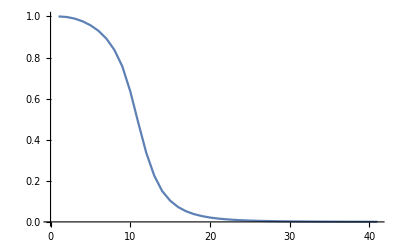

```mathematica
ListLinePlot[overlaps]
```

```mathematica
H.eigenvectors[[1]]
```

{-5.0874,2.56975×10^-8,-1.45119×10^-8,-0.66206,7.7088×10^-10,-0.21489,-0.66206,-1.17343×10^-10,1.73168×10^-8,-0.21489,-0.21489,1.17703×10^-9,-0.66206,9.64911×10^-9,-8.14583×10^-9,-0.105047,-2.65082×10^-8,-0.66206,-0.21489,-5.7401×10^-9,-0.21489,-7.22212×10^-9,3.5504×10^-9,-0.105047,-0.66206,8.14138×10^-9,-6.63701×10^-9,-0.105047,-6.34663×10^-9,-0.105047,-0.105047,-1.55858×10^-9}

```mathematica
L=4;(*Размер матрицы*)g=1;(*Параметр g*)J=0.5;(*Параметр J*)(*Генерация гамильтониана*)H=genHamiltonian[L,g,J];

(*Вычисление первых k собственных значений и собственных векторов*)
{k,m}={3,10};(*k-количество собственных значений,m-количество итераций в методе Ланцоша*){eigenvalues,eigenvectors}=Quiet@Eigensystem[H,k,Method->{"Arnoldi","Criteria"->"RealPart",(*"Shift"->1 ,*)"MaxIterations"->m}];
(*Вывод результатов*)
eigenvalues
eigenvectors;
v1 = eigenvectors[[1]].createSigmaX[L, 0];
v2 = createSigmaX[L, L/2].eigenvectors[[1]];
Abs[v1.v2];
```

{4.27156,3.23607,2.}

```mathematica
DeltaEn21 = Table[L=6;(*Размер матрицы*)g=gval;(*Параметр g*)J=0.5;(*Параметр J*)(*Генерация гамильтониана*)H=genHamiltonian[L,g,J];

(*Вычисление первых k собственных значений и собственных векторов*)
{k,m}={3,10};(*k-количество собственных значений,m-количество итераций в методе Ланцоша*)

{eigenvalues2,eigenvectors2}=Quiet@Eigensystem[H,k,Method->{"Arnoldi","Criteria"->"RealPart","Shift"->-50,"MaxIterations"->m}];
(*Вывод результатов*)
eigenvalues2 = Sort[eigenvalues2, Less];
eigenvalues2[[2]]-eigenvalues2[[1]], {gval, 0, 2, 0.01}];
```

```mathematica
DeltaEn31 = Table[L=6;(*Размер матрицы*)g=gval;(*Параметр g*)J=0.5;(*Параметр J*)(*Генерация гамильтониана*)H=genHamiltonian[L,g,J];

(*Вычисление первых k собственных значений и собственных векторов*)
{k,m}={3,10};(*k-количество собственных значений,m-количество итераций в методе Ланцоша*)

{eigenvalues2,eigenvectors2}=Quiet@Eigensystem[H,k,Method->{"Arnoldi","Criteria"->"RealPart","Shift"->-50,"MaxIterations"->m}];
(*Вывод результатов*)
eigenvalues2 = Sort[eigenvalues2, Less];
eigenvalues2[[3]]-eigenvalues2[[1]], {gval, 0, 2, 0.01}];
```

1.00689

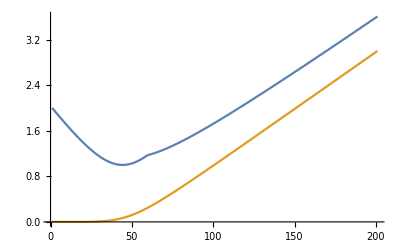

```mathematica
ListLinePlot[{DeltaEn31, DeltaEn21}]
```